```mathematica
ClearAll["Global`*"];
```

```mathematica
f[t_,y_]:=t*(y^2)^(1/3);
```

```mathematica
(*Функция отклонения*)
```

```mathematica
calculateDifference[basicU_,concreteU_,m_]:=(
Res=Table[0,{m+1}];
Do[
Res[[i]]=Abs[concreteU[[i,2]]-basicU[[i,2]]],{i,1,m}
];
Print["Максимальное отклонение: ",Max[Res]];
Print["Точность: ",(Max[Res]/(2^4-1))];
MatrixForm[N[Res]]
);
```

```mathematica
(*Метод Рунге-Кутта явный*)
```

```mathematica
explicitRunge[t0_, tk_, y0_, m_]:=(
k1[h_, t_, y_]:=f[t,y];
k2[h_, t_, y_]:=f[t+0.5*h,y+0.5*h*k1[h,t,y]];
k3[h_, t_, y_]:=f[t+0.5*h,y+0.5*h*k2[h,t,y]];
k4[h_, t_, y_]:=f[t+h,y+h*k3[h,t,y]];
Print["Число шагов: ", m];
h=(tk-t0)/m;
Print["Шаг: ", h];
U=Table[0, {m+1},{2}];
U[[1,1]]=t0;
U[[1,2]]=y0;
t=t0;
y=y0;
Do[
dy=h*(k1[h,t,y]+2*k2[h,t,y]+2*k3[h,t,y]+k4[h,t,y])/6;
t=t+h;
y=y+dy;
U[[i,1]]=t;
U[[i,2]]=y,
{i,2,m+1}];
p=ListLinePlot[U];
Print[p];
U
);
```

Число шагов: 10

Шаг: 1/10

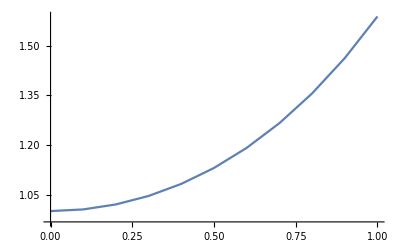

(0. | 1.
0.1 | 1.00501
0.2 | 1.02013
0.3 | 1.04568
0.4 | 1.08215
0.5 | 1.13028
0.6 | 1.19102
0.7 | 1.26555
0.8 | 1.35535
0.9 | 1.46214
1. | 1.58796)

```mathematica
basic=explicitRunge[0,1,1,10];
MatrixForm[N[basic]]
```

Число шагов: 15

Шаг: 1/15

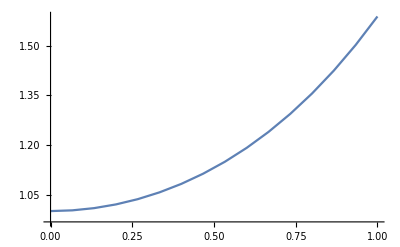

(0. | 1.
0.0666667 | 1.00222
0.133333 | 1.00892
0.2 | 1.02013
0.266667 | 1.03598
0.333333 | 1.05659
0.4 | 1.08215
0.466667 | 1.11289
0.533333 | 1.14907
0.6 | 1.19102
0.666667 | 1.23909
0.733333 | 1.29371
0.8 | 1.35535
0.866667 | 1.42453
0.933333 | 1.50185
1. | 1.58796)

```mathematica
current=explicitRunge[0,1,1,15];
MatrixForm[N[current]]
```

```mathematica
calculateDifference[basic,current,10]
```

Максимальное отклонение: 0.271119

Точность: 0.0180746

(0.
0.00278447
0.0112184
0.0255447
0.0461737
0.0736899
0.108864
0.152664
0.206276
0.271119
0.)

```mathematica
(*Метод Рунге-Кутта неявный*)
```

```mathematica
implicitRunge[t0_,tk_, yk_, m_]:=(
k1[h_, t_, y_]:=f[t,y];
k2[h_, t_, y_]:=f[t-0.5*h,y-0.5*h*k1[h,t,y]];
k3[h_, t_, y_]:=f[t-0.5*h,y-0.5*h*k2[h,t,y]];
k4[h_, t_, y_]:=f[t-h,y-h*k3[h,t,y]];
Print["Число шагов: ", m];
h=(tk-t0)/m;
Print["Шаг: ", h];
U=Table[0, {m+1},{2}];
U[[1,1]]=tk;
U[[1,2]]=yk;
t=tk;
y=yk;
Do[
dy=h*(k1[h,t,y]+2*k2[h,t,y]+2*k3[h,t,y]+k4[h,t,y])/6;
t=t-h;
y=y-dy;
U[[i,1]]=t;
U[[i,2]]=y,
{i,2,m+1}];
p=ListLinePlot[U];
Print[p];
U
);
```

Число шагов: 15

Шаг: 1/15

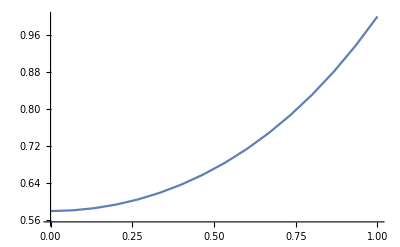

(1. | 1.
0.933333 | 0.93693
0.866667 | 0.880646
0.8 | 0.830584
0.733333 | 0.786236
0.666667 | 0.747149
0.6 | 0.71292
0.533333 | 0.683194
0.466667 | 0.657662
0.4 | 0.636056
0.333333 | 0.618148
0.266667 | 0.603748
0.2 | 0.592704
0.133333 | 0.584899
0.0666667 | 0.580248
0. | 0.578704)

```mathematica
implicitRes=implicitRunge[0,1,1,15];
MatrixForm[N[implicitRes]]
```

```mathematica
(* Метод Рунге-Кутта вложенный*)
```

```mathematica
nestedRunge[t0_,tk_, y0_, m_]:=(
k1[h_, t_, y_]:=f[t,y];
k2[h_, t_, y_]:=f[t+0.25*h,y+0.25*h*k1[h, t, y]];
k3[h_, t_, y_]:=f[t+(3/8)*h,y+(3/32)*h*k1[h, t, y]+(9/32)*h*k2[h, t, y]];
k4[h_, t_, y_]:=f[t+(12/13)*h,y+h*((1932/2197)*k1[h, t, y]-(7200/2197)*k2[h, t, y]+(7296/2197)*k3[h, t, y])];
k5[h_, t_, y_]:=f[t+h,y+h*((439/216)*k1[h, t, y]-8*k2[h, t, y]+(3680/513)*k3[h, t, y]-(845/4104)*k4[h, t, y])];
k6[h_, t_, y_]:=f[t+0.5*h,y-h*((8/27)*k1[h, t, y]+2*k2[h, t, y]-(3544/2565)*k3[h, t, y]+(1859/4104)*k4[h, t, y]-(11/40)*k5[h, t, y])];
Print["Число шагов: ",m];
h=(tk-t0)/m;
Print["Шаг: ",h];
t=t0;
y=y0;
U=Table[0,{m+1},{3}];
ForPlot=Table[0,{m+1},{2}];
U[[1,1]]=t0;
U[[1,2]]=y0;
U[[1,3]]=0;
ForPlot[[1,1]]=t0;
ForPlot[[1,2]]=y0;
Do[
dy=h*((25/216)*k1[h,t,y]*(1408/2565)*k3[h, t, y]+(2197/4104)*k4[h, t, y]-(1/5)*k5[h, t, y]);
t=t+h;
y=y+dy;
U[[i,1]]=t;
U[[i,2]]=y;
ForPlot[[i,1]]=t;
ForPlot[[i,2]]=y;
eps=h*(k1[h,t,y]/360-(128/4275)*k3[h,t,y]-(2197/75240)*k4[h,t,y]+k5[h,t,y]/50*(2/55)*k6[h,t,y]);
U[[i,3]]=eps,{i,2,m+1}];
p=ListLinePlot[ForPlot];
Print[p];
U
);
```

Число шагов: 15

Шаг: 1/15

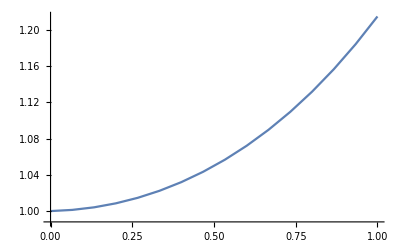

(0. | 1. | 0.
0.0666667 | 1.00131 | -0.000421161
0.133333 | 1.00415 | -0.000674265
0.2 | 1.00856 | -0.000929854
0.266667 | 1.01462 | -0.00118875
0.333333 | 1.02238 | -0.00145182
0.4 | 1.03192 | -0.00171994
0.466667 | 1.04331 | -0.00199407
0.533333 | 1.05666 | -0.00227519
0.6 | 1.07205 | -0.00256432
0.666667 | 1.0896 | -0.00286256
0.733333 | 1.10944 | -0.00317106
0.8 | 1.13169 | -0.00349103
0.866667 | 1.15652 | -0.00382376
0.933333 | 1.18411 | -0.00417063
1. | 1.21463 | -0.00453309)

```mathematica
nestedRed=nestedRunge[0,1,1,15];
MatrixForm[N[nestedRed]]
```

```mathematica
Clear[t,y];
```

```mathematica
(*Стандартный метод*)
```

```mathematica
explicitMathOp[t0_,tk_,y0_,m_]:=(
Y=NDSolve[{y'[t]==y[t]*(y[t]^2)^(1/3),y[t0]==0},y,{t,t0,tk},Method->"ExplicitRungeKutta"];
p=Plot[Evaluate[y[t]/.Y],{t,t0,tk}];
Print[p];
y[t_]=y[t]/.Y;
Print["Количество шагов: ",m];
h=(tk-t0)/m;
Print["Шаг: ",h];
t=t0;
U=Table[0,{m+1},{2}];
Do[
U[[i,1]]=t;
U[[i,2]]=y[t];
t+=h,
{i,1,m+1}
];
U
);
```

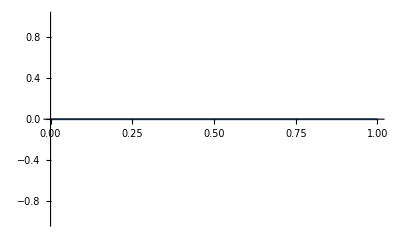

Количество шагов: 15

Шаг: 1/15

(0 | {0.}
1/15 | {0.}
2/15 | {0.}
1/5 | {0.}
4/15 | {0.}
1/3 | {0.}
2/5 | {0.}
7/15 | {0.}
8/15 | {0.}
3/5 | {0.}
2/3 | {0.}
11/15 | {0.}
4/5 | {0.}
13/15 | {0.}
14/15 | {0.}
1 | {0.})

```mathematica
explicitMRes=explicitMathOp[0,1,1,15];
MatrixForm[explicitMRes]
```

```mathematica
calculateDifference[current,explicitMRes,15]
```

Максимальное отклонение: 1.50185

Точность: 0.100123

({1.}
{1.00222}
{1.00892}
{1.02013}
{1.03598}
{1.05659}
{1.08215}
{1.11289}
{1.14907}
{1.19102}
{1.23909}
{1.29371}
{1.35535}
{1.42453}
{1.50185}
0.)

```mathematica
calculateDifference[Reverse[implicitRes],explicitMRes,15]
```

Максимальное отклонение: 0.93693

Точность: 0.062462

({0.578704}
{0.580248}
{0.584899}
{0.592704}
{0.603748}
{0.618148}
{0.636056}
{0.657662}
{0.683194}
{0.71292}
{0.747149}
{0.786236}
{0.830584}
{0.880646}
{0.93693}
0.)

```mathematica
calculateDifference[nestedRed,explicitMRes,15]
```

Максимальное отклонение: 1.18411

Точность: 0.0789404

({1.}
{1.00131}
{1.00415}
{1.00856}
{1.01462}
{1.02238}
{1.03192}
{1.04331}
{1.05666}
{1.07205}
{1.0896}
{1.10944}
{1.13169}
{1.15652}
{1.18411}
0.)

```mathematica
Clear[t,y];
```

```mathematica
implicitMathOp[t0_,tk_,y0_,m_]:=(
Y=NDSolve[{y'[t]==y[t]*(y[t]^2)^(1/3),y[t0]==0},y,{t,t0,tk},Method->"ImplicitRungeKutta"];
p=Plot[Evaluate[y[t]/.Y],{t,t0,tk}];
Print[p];
y[t_]=y[t]/.Y;
Print["Количество шагов: ",m];
h=(tk-t0)/m;
Print["Шаг: ",h];
t=t0;
U=Table[0,{m+1},{2}];
Do[
U[[i,1]]=t;
U[[i,2]]=y[t];
t+=h,
{i,1,m+1}
];
U
);
```

```mathematica
implicitMRes=implicitMathOp[0,1,1,15];
MatrixForm[explicitMRes]
```

-Graphics-

Количество шагов: 15

Шаг: 1/15

(0 | {0.}
1/15 | {0.}
2/15 | {0.}
1/5 | {0.}
4/15 | {0.}
1/3 | {0.}
2/5 | {0.}
7/15 | {0.}
8/15 | {0.}
3/5 | {0.}
2/3 | {0.}
11/15 | {0.}
4/5 | {0.}
13/15 | {0.}
14/15 | {0.}
1 | {0.})

```mathematica
calculateDifference[current,implicitMRes,15]
```

Максимальное отклонение: 1.50185

Точность: 0.100123

({1.}
{1.00222}
{1.00892}
{1.02013}
{1.03598}
{1.05659}
{1.08215}
{1.11289}
{1.14907}
{1.19102}
{1.23909}
{1.29371}
{1.35535}
{1.42453}
{1.50185}
0.)

```mathematica
calculateDifference[Reverse[implicitRes],implicitMRes,15]
```

Максимальное отклонение: 0.93693

Точность: 0.062462

({0.578704}
{0.580248}
{0.584899}
{0.592704}
{0.603748}
{0.618148}
{0.636056}
{0.657662}
{0.683194}
{0.71292}
{0.747149}
{0.786236}
{0.830584}
{0.880646}
{0.93693}
0.)

```mathematica
calculateDifference[nestedRed,explicitMRes,15]
```

Максимальное отклонение: 1.18411

Точность: 0.0789404

({1.}
{1.00131}
{1.00415}
{1.00856}
{1.01462}
{1.02238}
{1.03192}
{1.04331}
{1.05666}
{1.07205}
{1.0896}
{1.10944}
{1.13169}
{1.15652}
{1.18411}
0.)